# Computational Science

## Machine Learning for Physicists Project: Unsupervised and supervised analysis of protein sequences

This notebook is 100% human-made and has been created without any LLM.

Paul Cousin

Université Paris Cité • 2025/2026

## Note to the reader

Cells colored in blue will be code cells.

Cells colored in pink will be text comments.

## Import and format data

```mathematica
formatData[s_String]:=Module[{string=s},
string//=StringSplit[#,">"]&;
string//=StringDelete[#,"\n"]&;
string//=StringReplace[#,"sequence_"~~x:NumberString~~" functional_"~~y:("true"|"false")~~z__~~WordBoundary:>x~~","~~y~~","~~z]&;string//=StringSplit[#,","]&;
string/.{x_,y_,z_}:>{ToExpression@x,y=="true",z}
];
```

formatData is a function that formats the content of the .faa files which is encapsulated in  and  in the following cell.

```mathematica
natSeq=formatData@;
artSeq=formatData@;
```

Here is an example of how a sequence is now formatted.

```mathematica
natSeq[[1]]
```

{1,True,-TSENPLLALREKISALDEKLLALLAERRELAVEVGKAKLLSHRPVRDIDRERDLLERLITLGK-AHHLDAHYITRLFQLIIEDSVLTQQALLQQH}

## Task 1: One-hot encoding of protein sequence data

```mathematica
characterMap={"A"->1,"C"->2,"D"->3,"E"->4,"F"->5,"G"->6,"H"->7,"I"->8,"K"->9,"L"->10,"M"->11,"N"->12,"P"->13,"Q"->14,"R"->15,"S"->16,"T"->17,"V"->18,"W"->19,"Y"->20};
```

```mathematica
vectorize[seq_]:=SparseArray[If[#!="-",#->1,{}],20]&/@Replace[characterMap]/@StringPartition[seq,1];
```

```mathematica
natSeqHot=SparseArray[vectorize/@natSeq[[;;,3]]];
artSeqHot=SparseArray[vectorize/@artSeq[[;;,3]]];
```

All the sequences have been one-hot encoded in the SparseArray format.

```mathematica
natSeqHot[[1]]
```

SparseArray[…]

```mathematica
ArrayPlot@Transpose@natSeqHot[[1]]
```

-Graphics-

## Task 2: Dimensional reduction and visualization of sequence space

The data is now stored in a 3-dimensional tensor. Its dimensions are:

```mathematica
Dimensions@natSeqHot
```

{1130,96,20}

We need to create a 1130×1130 covariance matrix from this data. We therefore need a way to combine two 96×20 matrices together and obtain a measure of their similitude. The simplest way is probably to count the number of elements the two matrices have in common by multiplying them term-by-term and computing the total. For example:

```mathematica
Total[natSeqHot[[1]]*natSeqHot[[2]],2]
```

23

The covariance matrix corresponds to the symmetric matrix where all sequences are compared to each other in this way.

```mathematica
covMatNat=Table[Total[natSeqHot[[i]]*natSeqHot[[j]],2],{i,1130},{j,1130}];
```

```mathematica
ArrayPlot[covMatNat,ColorFunction->"BlueGreenYellow",PlotLabel->"Covariance Matrix of the Natural Sequences"]
```

-Graphics-

Using the first eigenvalues and eigenvectors of this covariance matrix, we can project our data on the two or three most meaningful axes. For this purpose we can use the Eigenvectors function which will return the first eigenvectors sorted by eigenvalues. Here we will compute only three.

```mathematica
eigVecNat=Eigenvectors[N@covarianceMatrix,3];
```

We can now project all the data points onto these eigenvectors.

```mathematica
projection[seq_]:=Total[Total[eigVecNat[[#]]*natSeqHot]*seq,2]&/@{1,2,3};
```

```mathematica
projectedNat=projection/@natSeqHot;
```

To separate the functional and non-functional sequence, we need the indices correspond to each in the original lists.

```mathematica
funtionalNatSeqIndices=Cases[natSeq,x_?(#[[2]]&):>x[[1]]];
nonFuntionalNatSeqIndices=Complement[Range@Length@natSeq,funtionalNatSeqIndices];
funtionalArtSeqIndices=Cases[artSeq,x_?(#[[2]]&):>x[[1]]];
nonFuntionalArtSeqIndices=Complement[Range@Length@artSeq,funtionalArtSeqIndices];
```

Let’s plot the result, first in 2D.

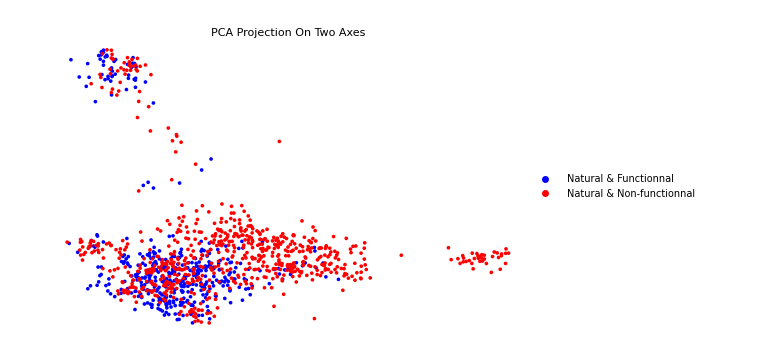

```mathematica
plotNat2D=ListPlot[projectedNat[[#,;;2]]&/@{funtionalNatSeqIndices,nonFuntionalNatSeqIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Blue,Red},PlotLabel->"PCA Projection On Two Axes",PlotLegends-> {"Natural & Functionnal","Natural & Non-functionnal"}]
```

The following 3D plot is interactive and can be manipulated.

```mathematica
plotNat3D=ListPointPlot3D[projectedNat[[#]]&/@{funtionalNatSeqIndices,nonFuntionalNatSeqIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Blue,Red},PlotLabel->"PCA Projection On Three Axes",PlotLegends-> {"Natural & Functionnal","Natural & Non-functionnal"}]
```

-Graphics3D-

Let’s now look at the artificial sequences projected on the previously computed vectors.

```mathematica
projectedArt=projection/@artSeqHot;
```

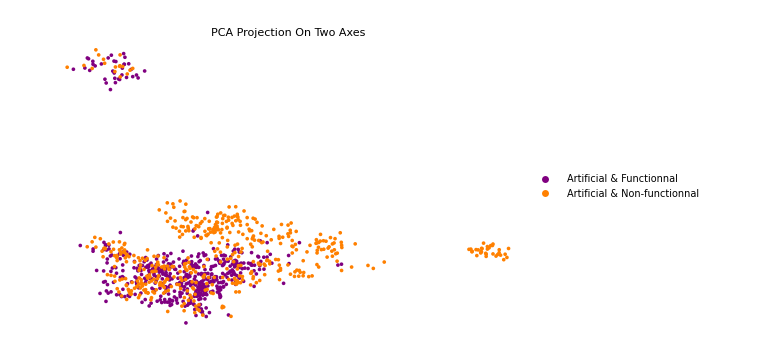

```mathematica
plotArt2D=ListPlot[projectedArt[[#,;;2]]&/@{funtionalArtSeqIndices,nonFuntionalArtSeqIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Purple,Orange},PlotLabel->"PCA Projection On Two Axes",PlotLegends-> {"Artificial & Functionnal","Artificial & Non-functionnal"}]
```

```mathematica
plotArt3D=ListPointPlot3D[projectedArt[[#]]&/@{funtionalArtSeqIndices,nonFuntionalArtSeqIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Purple,Orange},PlotLabel->"PCA Projection On Three Axes",PlotLegends-> {"Artificial & Functionnal","Artificial & Non-functionnal"}]
```

-Graphics3D-

To see the similarities more clearly let’s plot all sequences together.

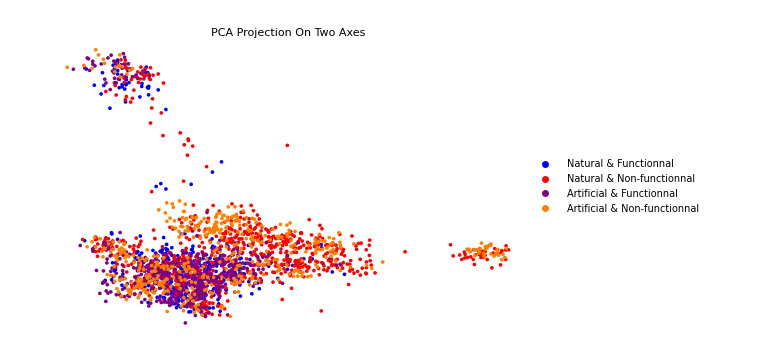

```mathematica
Show[{plotNat2D,plotArt2D},PlotRange->All]
```

```mathematica
Show[{plotNat3D,plotArt3D},PlotRange->All]
```

-Graphics3D-

In the case of both natural and artificial sequences, we see regions that are clearly non-functional and other regions in which a mixture of functional and non-functional sequences coexist.

## Task 3: Clustering sequence data